### L 4.7

```mathematica
T[d_] = 1.44/Abs[Exp[-I*k1] - Exp[4.996I]*Exp[I*k1]]^2;
```

```mathematica
data = ({{0.2, 32}, {1/2, 28.1}, {1, 16.5}, {3/2, 11}, {2, 6.2}, {5/2, 2.2}, {3, 1.9}, {7/2, 0.04}, {4, 0.002}});
```

```mathematica
adjustedData  =Transpose[data][[2]]/32
```

{1,0.878125,0.515625,11/32,0.19375,0.06875,0.059375,0.00125,0.0000625}

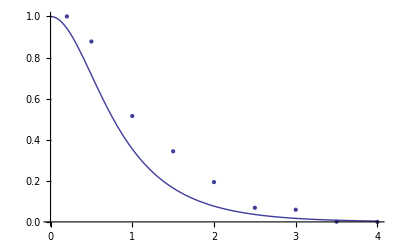

```mathematica
Show[{ListPlot[Transpose[{Transpose[data][[1]],adjustedData}]]},Plot[T[d],{d,0,4}]]
```